# Rigid rotation of a spin-helix state in the open XXZ chain

Purpose: decide, by exact construction and by direct real-time simulation, whether an initial spin-helix product state of the open, finite XXZ chain can rotate rigidly about the z axis, i.e. whether psi(t) = (global phase) x helix(q, theta, phi0 + w t) for all t.
Organization: Section 1 fixes the model and conventions, Section 2 defines the helix states and their free parameters, Section 3 derives and tests the parameter choice that supports a rigid rotation, Section 4 integrates the Schroedinger equation in the laboratory frame and produces the plots. Each section contains its own definitions and its own VerificationTest block. Sections are meant to be evaluated in order: Section k uses the definitions of Sections 1, ..., k-1 only.

## 1. Conventions for the open XXZ model

Hilbert space: n spins 1/2, site 1 is the leftmost tensor factor, local basis {|up>, |down>} = {|0>, |1>}, S^a_j = sigma^a_j / 2, hbar = 1.
Hamiltonian (spin convention):
H = J Sum_{j=1}^{n-1} (S^x_j S^x_{j+1} + S^y_j S^y_{j+1} + Delta S^z_j S^z_{j+1}) + hL . S_1 + hR . S_n + hz S^z_tot.
hL and hR are arbitrary 3-vectors acting on the two edge spins only; hz is a uniform longitudinal field. The bulk part commutes with S^z_tot; arbitrary edge fields do not.

```mathematica
SpinOperator[a_Integer, j_Integer, n_Integer] := KroneckerProduct[IdentityMatrix[2^(j - 1), SparseArray], SparseArray[PauliMatrix[a]/2], IdentityMatrix[2^(n - j), SparseArray]];

XXZBulkHamiltonian[J_, delta_, n_Integer] := SparseArray[{}, {2^n, 2^n}] + J Sum[SpinOperator[1, j, n] . SpinOperator[1, j + 1, n] + SpinOperator[2, j, n] . SpinOperator[2, j + 1, n] + delta SpinOperator[3, j, n] . SpinOperator[3, j + 1, n], {j, 1, n - 1}];

EdgeFieldOperator[h_List, j_Integer, n_Integer] := Sum[h[[a]] SpinOperator[a, j, n], {a, 3}];

TotalSzOperator[n_Integer] := SparseArray[Band[{1, 1}] -> Table[n/2 - DigitCount[b, 2, 1], {b, 0, 2^n - 1}], {2^n, 2^n}];

OpenXXZHamiltonian[J_, delta_, n_Integer, hL_List, hR_List, hz_] := XXZBulkHamiltonian[J, delta, n] + EdgeFieldOperator[hL, 1, n] + EdgeFieldOperator[hR, n, n] + hz TotalSzOperator[n];
```

Rotations about z. U(alpha) = exp(-i alpha S^z_tot) is diagonal in the computational basis. Because the bulk is U(1) invariant and S^a transforms as a vector, U(alpha) H(hL, hR) U(alpha)^dagger = H(R_z(alpha) hL, R_z(alpha) hR): a rotation of the state is equivalent to a rotation of the two edge fields. This identity is the backbone of Section 3.

```mathematica
ZRotationOperator[alpha_, n_Integer] := SparseArray[Band[{1, 1}] -> Table[Exp[-I alpha (n/2 - DigitCount[b, 2, 1])], {b, 0, 2^n - 1}], {2^n, 2^n}];

RotateAboutZ[v_List, alpha_] := RotationMatrix[alpha, {0, 0, 1}] . v;

LocalSpinOperators[n_Integer] := LocalSpinOperators[n] = Table[N[SpinOperator[a, j, n]], {j, n}, {a, 3}];

LocalSpinExpectations[psi_List, n_Integer] := Map[Re[Conjugate[psi] . (# . psi)] &, LocalSpinOperators[n], {2}];
```

### Tests of the conventions

Checked: Hermiticity, normalization of one bond in the user's matrix form (J/4){{Delta,0,0,0},{0,-Delta,2,0},{0,2,-Delta,0},{0,0,0,Delta}}, energy of the fully polarized state, U(1) invariance of the bulk, the rotation-covariance identity above, and the closed form of U(alpha).

```mathematica
Module[{n = 4, J = 1.3, delta = 0.37, hL = {0.3, -0.7, 0.2}, hR = {-0.4, 0.1, 0.9}, hz = 0.25, alpha = 0.81, h},
  h = OpenXXZHamiltonian[J, delta, n, hL, hR, hz];
  TestReport[{
    VerificationTest[Max[Abs[h - ConjugateTranspose[h]]], 0., SameTest -> (Abs[#1 - #2] < 10^-12 &), TestID -> "Hermiticity"],
    VerificationTest[Normal[XXZBulkHamiltonian[J, delta, 2]], J/4 {{delta, 0, 0, 0}, {0, -delta, 2, 0}, {0, 2, -delta, 0}, {0, 0, 0, delta}}, SameTest -> (Max[Abs[#1 - #2]] < 10^-12 &), TestID -> "Bond normalization"],
    VerificationTest[Normal[XXZBulkHamiltonian[J, delta, n]][[1, 1]], J delta (n - 1)/4, SameTest -> (Abs[#1 - #2] < 10^-12 &), TestID -> "Polarized energy"],
    VerificationTest[Max[Abs[XXZBulkHamiltonian[J, delta, n] . TotalSzOperator[n] - TotalSzOperator[n] . XXZBulkHamiltonian[J, delta, n]]], 0., SameTest -> (Abs[#1 - #2] < 10^-12 &), TestID -> "Bulk U(1) symmetry"],
    VerificationTest[Max[Abs[N[ZRotationOperator[alpha, n] . h . ConjugateTranspose[ZRotationOperator[alpha, n]]] - OpenXXZHamiltonian[J, delta, n, RotateAboutZ[hL, alpha], RotateAboutZ[hR, alpha], hz]]], 0., SameTest -> (Abs[#1 - #2] < 10^-12 &), TestID -> "Rotation covariance"],
    VerificationTest[Max[Abs[Normal[N[ZRotationOperator[alpha, n]]] - MatrixExp[-I alpha Normal[N[TotalSzOperator[n]]]]]], 0., SameTest -> (Abs[#1 - #2] < 10^-12 &), TestID -> "Closed form of U(alpha)"]
  }]
]
```

TestReportObject[…]

## 2. Helix states and their free parameters

Definition (product state, no entanglement):
|psi(q, theta, phi)> = Tensor_{j=1}^{n} [ cos(theta/2) |up> + exp(i (phi + (j-1) q)) sin(theta/2) |down> ].
Free parameters:
n: number of sites.
q: azimuthal winding per bond (pitch 2 Pi / q sites).
theta: common polar angle; <S^z_j> = cos(theta)/2 and |<S^perp_j>| = sin(theta)/2 for every j.
phi: azimuth of site 1; site j points along phi_j = phi + (j-1) q.
Sign convention: with |up> = |0> and the phase exp(i alpha) on the |down> component, the local Bloch vector is (sin theta cos alpha, sin theta sin alpha, cos theta), i.e. the azimuth increases with j for q > 0. The test "Spin profile and Bloch-vector sign" checks this numerically.

```mathematica
HelixSpinor[theta_, alpha_] := {Cos[theta/2], Exp[I alpha] Sin[theta/2]};

HelixState[n_Integer, q_, theta_, phi_] := Flatten[KroneckerProduct @@ Table[HelixSpinor[theta, phi + (j - 1) q], {j, n}]];

BlochUnitVector[theta_, alpha_] := {Sin[theta] Cos[alpha], Sin[theta] Sin[alpha], Cos[theta]};

HelixAzimuths[n_Integer, q_, phi_] := Table[phi + (j - 1) q, {j, n}];

HelixSpinProfile[n_Integer, q_, theta_, phi_] := Table[BlochUnitVector[theta, phi + (j - 1) q]/2, {j, n}];

HelixSectorWeights[n_Integer, theta_] := Table[{n/2 - k, Binomial[n, k] Cos[theta/2]^(2 (n - k)) Sin[theta/2]^(2 k)}, {k, 0, n}];

HelixFreeParameters[n_Integer, q_, theta_, phi_] := <|"Sites" -> n, "Winding q" -> q, "Pitch 2Pi/q" -> 2 Pi/q, "Polar angle theta" -> theta, "Initial azimuth phi" -> phi, "<S^z_j>" -> Cos[theta]/2, "|<S^perp_j>|" -> Sin[theta]/2, "<S^z_tot>" -> n Cos[theta]/2, "Var S^z_tot" -> n Sin[theta]^2/4|>;
```

HelixSectorWeights lists the weight of the helix in each S^z_tot = m sector. A rotation exp(-i alpha S^z_tot) multiplies the sector-m component by exp(-i alpha m), so a rigid rotation at angular velocity w is the statement that the sector components acquire only the relative phases exp(-i w m t). Var S^z_tot = n sin^2(theta)/4 controls how fast any mismatch between those phases destroys the overlap.

### Tests of the helix definitions

```mathematica
Module[{n = 5, q = 0.7, theta = 0.9, phi = 0.3, alpha = 1.234, psi},
  psi = N[HelixState[n, q, theta, phi]];
  TestReport[{
    VerificationTest[Norm[psi], 1., SameTest -> (Abs[#1 - #2] < 10^-12 &), TestID -> "Normalization"],
    VerificationTest[LocalSpinExpectations[psi, n], N[HelixSpinProfile[n, q, theta, phi]], SameTest -> (Max[Abs[#1 - #2]] < 10^-12 &), TestID -> "Spin profile and Bloch-vector sign"],
    VerificationTest[N[ZRotationOperator[alpha, n]] . psi, Exp[-I n alpha/2] N[HelixState[n, q, theta, phi + alpha]], SameTest -> (Max[Abs[#1 - #2]] < 10^-12 &), TestID -> "Rotation shifts phi"],
    VerificationTest[Normal[Values[GroupBy[Transpose[{Normal[Diagonal[TotalSzOperator[n]]], Abs[psi]^2}], First -> Last, Total]]], N[Reverse[HelixSectorWeights[n, theta]][[All, 2]]], SameTest -> (Max[Abs[Sort[#1] - Sort[#2]]] < 10^-12 &), TestID -> "Sector weights"],
    VerificationTest[Re[Conjugate[psi] . (N[TotalSzOperator[n]] . N[TotalSzOperator[n]] . psi)] - Re[Conjugate[psi] . (N[TotalSzOperator[n]] . psi)]^2, N[n Sin[theta]^2/4], SameTest -> (Abs[#1 - #2] < 10^-12 &), TestID -> "Var S^z_tot"]
  }]
]
```

TestReportObject[…]

```mathematica
HelixFreeParameters[6, Pi/3, 1.1, 0] // Dataset
```

## 3. Parameters that support a rigid helix

### 3.1 Static step: the helix as an exact eigenstate

For a product state with constant theta and constant winding q, the bulk residual of every bond cancels in the telescoping sum iff Delta = cos q, leaving two uncompensated terms localized on sites 1 and n. They are removed by the matched edge fields
hL = -(J sin q sin theta / 2) t(phi) + bL n(theta, phi),
hR = +(J sin q sin theta / 2) t(phi_n) + bR n(theta, phi_n),   phi_n = phi + (n-1) q,
with t(alpha) = (-sin alpha, cos alpha, 0) the azimuthal tangent and n(theta, alpha) the local Bloch direction. bL and bR are free: a field parallel to the local spin only shifts the energy. Then H(hL, hR, hz = 0) |psi> = E_h |psi>, E_h = J (n-1) cos q / 4 + (bL + bR)/2.

```mathematica
AzimuthalTangent[alpha_] := {-Sin[alpha], Cos[alpha], 0};

MatchedEdgeFields[J_, q_, theta_, phi_, n_Integer, bL_, bR_] := {-J Sin[q] Sin[theta]/2 AzimuthalTangent[phi] + bL BlochUnitVector[theta, phi], J Sin[q] Sin[theta]/2 AzimuthalTangent[phi + (n - 1) q] + bR BlochUnitVector[theta, phi + (n - 1) q]};

StaticHelixEnergy[J_, q_, n_Integer, bL_, bR_] := J (n - 1) Cos[q]/4 + (bL + bR)/2;
```

### 3.2 Dynamic step: co-rotating fields and the rotating frame

A static field cannot make the helix rotate: an eigenstate only acquires a phase. Rotation requires the edge fields themselves to turn. Take the matched fields at the moving azimuth phi0 + w t (w = FieldOmega). Because both t(alpha) and n(theta, alpha) are covariant, MatchedEdgeFields[.., phi0 + w t, ..] = R_z(w t) MatchedEdgeFields[.., phi0, ..], and by Section 1
H(t) = U(w t) H(0) U(w t)^dagger,   U(a) = exp(-i a S^z_tot).
Writing psi(t) = U(w t) chi(t) gives i d chi/dt = G chi with the time-independent rotating-frame generator
G = H(0) - w S^z_tot = H_XXZ + hL(phi0) . S_1 + hR(phi0) . S_n + (hz - w) S^z_tot.
Exact solution: psi(t) = U(w t) exp(-i G t) psi(0).
Rigidity criterion. psi(t) = (phase) U(w t) psi(0), i.e. the helix turns rigidly together with the fields, iff chi(t) = (phase) psi(0), i.e. iff psi(0) is an eigenvector of G. With Delta = cos q and matched fields, psi(0) is an eigenvector of H_XXZ + hL(phi0) . S_1 + hR(phi0) . S_n but not of S^z_tot (for 0 < theta < Pi), so the remaining condition is
hz = w.
Then psi(t) = exp(-i E_h t) exp(-i n w t/2) |psi(q, theta, phi0 + w t)>: exactly rigid, at angular velocity w = hz, with all spins keeping |<S_j>| = 1/2.
Scope of the statement: it covers rotation locked to the fields. A rigid rotation at some other rate is not excluded by this argument; the BestFidelity diagnostic of Section 4 (maximum over all rotation angles) tests for it numerically.
The four protocols below isolate each ingredient:
A: co-rotating matched fields with hz = w (all conditions met).
B: static matched fields plus hz (the bulk would precess, the edges are pinned).
C: co-rotating matched fields with hz = 0 (the edges are dragged, the bulk is not).
D: free ends plus hz (uniform Larmor precession on top of the non-stationary free-end dynamics).

```mathematica
HelixProtocol[n_Integer, J_, q_, theta_, phi0_, bL_, bR_, delta_, hz_, omega_, edgeFields_] := <|"L" -> n, "J" -> J, "q" -> q, "theta" -> theta, "phi0" -> phi0, "bL" -> bL, "bR" -> bR, "Delta" -> delta, "hz" -> hz, "FieldOmega" -> omega, "EdgeFields" -> edgeFields|>;

RigidRotationProtocol[n_Integer, J_, q_, theta_, phi0_, bL_, bR_, omega_] := HelixProtocol[n, J, q, theta, phi0, bL, bR, Cos[q], omega, omega, True];

ProtocolFields[p_Association, t_] := If[TrueQ[p["EdgeFields"]], MatchedEdgeFields[p["J"], p["q"], p["theta"], p["phi0"] + p["FieldOmega"] t, p["L"], p["bL"], p["bR"]], {{0, 0, 0}, {0, 0, 0}}];

ProtocolHamiltonian[p_Association, t_] := With[{f = ProtocolFields[p, t]}, OpenXXZHamiltonian[p["J"], p["Delta"], p["L"], f[[1]], f[[2]], p["hz"]]];

RotatingFrameGenerator[p_Association] := ProtocolHamiltonian[p, 0] - p["FieldOmega"] TotalSzOperator[p["L"]];

ExactState[p_Association, psi0_List, t_] := N[ZRotationOperator[p["FieldOmega"] t, p["L"]]] . MatrixExp[-I t Normal[N[RotatingFrameGenerator[p]]], psi0];

ExactTrajectory[p_Association, psi0_List, tMax_, nT_Integer] := Module[{m = N[Normal[Diagonal[TotalSzOperator[p["L"]]]]], u, chi}, u = MatrixExp[-I (tMax/nT) Normal[N[RotatingFrameGenerator[p]]]]; chi = NestList[u . # &, N[psi0], nT]; MapThread[Exp[-I p["FieldOmega"] #1 m] #2 &, {Subdivide[0., tMax, nT], chi}]];

RigidHelixPrediction[p_Association, t_] := Exp[-I StaticHelixEnergy[p["J"], p["q"], p["L"], p["bL"], p["bR"]] t] Exp[-I p["L"] p["FieldOmega"] t/2] HelixState[p["L"], p["q"], p["theta"], p["phi0"] + p["FieldOmega"] t];

RigidityDiagnostics[p_Association] := Module[{psi = N[HelixState[p["L"], p["q"], p["theta"], p["phi0"]]], g = N[RotatingFrameGenerator[p]], e}, e = Re[Conjugate[psi] . (g . psi)]; <|"Delta - Cos[q]" -> N[p["Delta"] - Cos[p["q"]]], "hz - FieldOmega" -> N[p["hz"] - p["FieldOmega"]], "RotatingFrameResidual" -> Norm[g . psi - e psi], "RotatingFrameEnergy" -> e|>];
```

RotatingFrameResidual = || G psi0 - <G> psi0 || vanishes iff the helix co-rotates rigidly with the fields. It is the single number that decides the question for a given protocol; Section 4 confirms it by brute-force integration in the laboratory frame, where nothing about the rotating frame is assumed.

### Tests of the rigidity conditions

```mathematica
Module[{n = 5, J = 1.3, q = 0.7, theta = 0.9, phi = 0.3, bL = 0.4, bR = -0.2, w = 0.6, alpha = 0.77, t = 1.7, f, h, psi, p},
  f = N[MatchedEdgeFields[J, q, theta, phi, n, bL, bR]];
  h = OpenXXZHamiltonian[J, Cos[q], n, f[[1]], f[[2]], 0];
  psi = N[HelixState[n, q, theta, phi]];
  p = RigidRotationProtocol[n, J, q, theta, phi, bL, bR, w];
  TestReport[{
    VerificationTest[Norm[h . psi - StaticHelixEnergy[J, q, n, bL, bR] psi], 0., SameTest -> (Abs[#1 - #2] < 10^-12 &), TestID -> "Static helix eigenstate, E_h"],
    VerificationTest[Norm[OpenXXZHamiltonian[J, Cos[q] + 0.05, n, f[[1]], f[[2]], 0] . psi - StaticHelixEnergy[J, q, n, bL, bR] psi] > 10^-3, True, TestID -> "Delta != cos q breaks the eigenstate"],
    VerificationTest[N[MatchedEdgeFields[J, q, theta, phi + alpha, n, bL, bR]], N[RotateAboutZ[#, alpha] & /@ MatchedEdgeFields[J, q, theta, phi, n, bL, bR]], SameTest -> (Max[Abs[#1 - #2]] < 10^-12 &), TestID -> "Field covariance"],
    VerificationTest[Max[Abs[N[ProtocolHamiltonian[p, t]] - N[ZRotationOperator[w t, n] . ProtocolHamiltonian[p, 0] . ConjugateTranspose[ZRotationOperator[w t, n]]]]], 0., SameTest -> (Abs[#1 - #2] < 10^-12 &), TestID -> "H(t) = U H(0) U^dagger"],
    VerificationTest[RigidityDiagnostics[p]["RotatingFrameResidual"], 0., SameTest -> (Abs[#1 - #2] < 10^-12 &), TestID -> "Rotating-frame eigenstate"],
    VerificationTest[ExactState[p, psi, t], N[RigidHelixPrediction[p, t]], SameTest -> (Max[Abs[#1 - #2]] < 10^-10 &), TestID -> "Exact rigid solution with phase"],
    VerificationTest[Last[ExactTrajectory[Append[p, "hz" -> w + 0.3], psi, 3 t, 30]], ExactState[Append[p, "hz" -> w + 0.3], psi, 3 t], SameTest -> (Max[Abs[#1 - #2]] < 10^-10 &), TestID -> "ExactTrajectory = ExactState"],
    VerificationTest[RigidityDiagnostics[Append[p, "hz" -> w + 0.1]]["RotatingFrameResidual"], 0.1 Sqrt[n] Sin[theta]/2, SameTest -> (Abs[#1 - #2] < 10^-12 &), TestID -> "Detuning residual = |hz - w| Sqrt[Var S^z]"]
  }]
]
```

TestReportObject[…]

## 4. Dynamics and plots

### 4.1 Laboratory-frame integrator and diagnostics

The laboratory-frame evolution solves i d psi/dt = H(t) psi with NDSolve, without using the rotating frame. Since the rotated fields are R_z(w t) h(0), the edge operator splits exactly as C0 + cos(w t) C1 + sin(w t) C2, where C0 contains the z components (which do not rotate), C1 the x, y components at t = 0, and C2 the same components rotated by Pi/2.

```mathematica
EdgeFieldDecomposition[p_Association] := Module[{f = N[ProtocolFields[p, 0]], n = p["L"]}, {EdgeFieldOperator[{0, 0, f[[1, 3]]}, 1, n] + EdgeFieldOperator[{0, 0, f[[2, 3]]}, n, n], EdgeFieldOperator[{f[[1, 1]], f[[1, 2]], 0}, 1, n] + EdgeFieldOperator[{f[[2, 1]], f[[2, 2]], 0}, n, n], EdgeFieldOperator[{-f[[1, 2]], f[[1, 1]], 0}, 1, n] + EdgeFieldOperator[{-f[[2, 2]], f[[2, 1]], 0}, n, n]}];

LabFrameEvolution[p_Association, psi0_List, tMax_] := Module[{n = p["L"], w = p["FieldOmega"], c, h0, c1, c2, x, t}, c = Normal[N[EdgeFieldDecomposition[p]]]; h0 = Normal[N[XXZBulkHamiltonian[p["J"], p["Delta"], n] + p["hz"] TotalSzOperator[n]]] + c[[1]]; c1 = c[[2]]; c2 = c[[3]]; NDSolveValue[{x'[t] == -I (h0 + Cos[w t] c1 + Sin[w t] c2) . x[t], x[0] == N[psi0]}, x, {t, 0, tMax}, Method -> {"ExplicitRungeKutta", "DifferenceOrder" -> 8}, AccuracyGoal -> 13, PrecisionGoal -> 13, MaxSteps -> Infinity, InterpolationOrder -> All]];
```

Diagnostics along the trajectory:
RigidFidelity: F(t) = |<psi(q, theta, phi0 + hz t)|psi(t)>|^2, the overlap with the helix rotated at the Larmor frequency hz.
BestFidelity: the maximum over all rotation angles a of |<U(a) psi0|psi(t)>|^2, computed from the S^z_tot sector decomposition; it is 1 iff psi(t) is some rotated copy of the initial helix, at whatever rate.
IntegratorError: max_t || psi_lab(t) - psi_exact(t) ||, comparing NDSolve with the rotating-frame solution of Section 3 (ExactTrajectory evaluates that solution on a uniform time grid with a single matrix exponential).
Local observables: <S_j(t)>, unwrapped azimuths, transverse length and S^z per site, and the Bloch-vector length 2|<S_j>| (equal to 1 iff spin j is unentangled from the rest).

```mathematica
UnwrapPhases[list_List] := FoldList[#1 + Mod[#2 - #1, 2 Pi, -Pi] &, First[list], Rest[list]];

BestRotationFidelity[p_Association, psi_List] := Module[{psi0 = N[HelixState[p["L"], p["q"], p["theta"], p["phi0"]]], m = Normal[Diagonal[TotalSzOperator[p["L"]]]], c, k, v, g, as, f, a0}, c = GroupBy[Transpose[{m, Conjugate[psi0] psi}], First -> Last, Total]; k = N[Keys[c]]; v = Values[c]; g = Function[x, Abs[Exp[I Outer[Times, x, k]] . v]^2]; as = Subdivide[0., 2 Pi, 360]; f = g[as]; a0 = as[[First[Ordering[f, -1]]]]; Do[as = a0 + Subdivide[-1., 1., 40] (2 Pi/360)/20^(r - 1); f = g[as]; a0 = as[[First[Ordering[f, -1]]]], {r, 1, 6}]; Max[f]];

Simulate[p_Association, tMax_, nT_Integer] := Module[{psi0 = N[HelixState[p["L"], p["q"], p["theta"], p["phi0"]]], sol, ts, states, pred, exact}, sol = LabFrameEvolution[p, psi0, tMax]; ts = Subdivide[0., tMax, nT]; states = sol /@ ts; pred = Table[N[HelixState[p["L"], p["q"], p["theta"], p["phi0"] + p["hz"] t]], {t, ts}]; exact = ExactTrajectory[p, psi0, tMax, nT]; <|"Parameters" -> p, "Times" -> ts, "States" -> states, "Spins" -> (LocalSpinExpectations[#, p["L"]] & /@ states), "RigidFidelity" -> MapThread[Abs[Conjugate[#1] . #2]^2 &, {pred, states}], "BestFidelity" -> (BestRotationFidelity[p, #] & /@ states), "IntegratorError" -> Max[MapThread[Norm[#1 - #2] &, {states, exact}]]|>];

SpinAzimuths[sim_Association] := Transpose[UnwrapPhases /@ Transpose[Map[Arg[#[[1]] + I #[[2]]] &, sim["Spins"], {2}]]];

BlochLengths[sim_Association] := Map[2 Norm[#] &, sim["Spins"], {2}];

SimulationSummary[sim_Association] := Module[{az = SpinAzimuths[sim], ts = sim["Times"], w = sim["Parameters"]["hz"]}, <|"RotatingFrameResidual" -> RigidityDiagnostics[sim["Parameters"]]["RotatingFrameResidual"], "max(1 - F_rigid)" -> Max[1 - sim["RigidFidelity"]], "max(1 - F_best)" -> Max[1 - sim["BestFidelity"]], "min Bloch length (edges)" -> Min[BlochLengths[sim][[All, {1, -1}]]], "max |phi_j(t) - phi_j(0) - hz t|" -> Max[Abs[(az - ConstantArray[First[az], Length[ts]]) - Outer[Times, w ts, ConstantArray[1, Length[First[az]]]]]], "IntegratorError" -> sim["IntegratorError"]|>];
```

### 4.2 Plotting functions

```mathematica
AzimuthPlot[sim_Association] := Module[{ts = sim["Times"], az = SpinAzimuths[sim], n = sim["Parameters"]["L"], w = sim["Parameters"]["hz"]}, ListLinePlot[Append[Table[Transpose[{ts, az[[All, j]] - az[[1, j]]}], {j, n}], Transpose[{ts, w ts}]], PlotStyle -> Append[Table[ColorData[97][j], {j, n}], Directive[Black, Dashed, Thick]], PlotLegends -> Append[Table["j = " <> ToString[j], {j, n}], "hz t"], Frame -> True, FrameLabel -> {"t", "ϕ_j(t) - ϕ_j(0)"}, PlotRange -> All, ImageSize -> 420]];

InfidelityPlot[sims_List, labels_List, key_String] := ListLogPlot[Table[Transpose[{s["Times"], Clip[1 - s[key], {10^-16, 1}]}], {s, sims}], Joined -> True, PlotLegends -> labels, PlotRange -> {10^-16, 2}, Frame -> True, FrameLabel -> {"t", "1 - " <> key}, ImageSize -> 420];

SiteObservablesPlot[sim_Association] := Module[{ts = sim["Times"], s = sim["Spins"], n = sim["Parameters"]["L"], th = sim["Parameters"]["theta"]}, Row[{ListLinePlot[Append[Table[Transpose[{ts, s[[All, j, 3]]}], {j, n}], Transpose[{ts, ConstantArray[Cos[th]/2, Length[ts]]}]], PlotStyle -> Append[Table[ColorData[97][j], {j, n}], Directive[Black, Dashed]], Frame -> True, FrameLabel -> {"t", "<S^z_j>"}, PlotRange -> {-0.55, 0.55}, ImageSize -> 280], ListLinePlot[Append[Table[Transpose[{ts, Norm /@ s[[All, j, 1 ;; 2]]}], {j, n}], Transpose[{ts, ConstantArray[Sin[th]/2, Length[ts]]}]], PlotStyle -> Append[Table[ColorData[97][j], {j, n}], Directive[Black, Dashed]], Frame -> True, FrameLabel -> {"t", "|<S^⊥_j>|"}, PlotRange -> {0, 0.55}, ImageSize -> 280], ListLinePlot[Table[Transpose[{ts, BlochLengths[sim][[All, j]]}], {j, n}], PlotStyle -> Table[ColorData[97][j], {j, n}], Frame -> True, FrameLabel -> {"t", "2|<S_j>|"}, PlotRange -> {0, 1.05}, ImageSize -> 280, PlotLegends -> Table["j = " <> ToString[j], {j, n}]]}, "  "]];

HelixSnapshot[sim_Association, k_Integer] := Module[{s = sim["Spins"][[k]], n = sim["Parameters"]["L"], d = 1.5, tips}, tips = Table[{0, 0, d j} + 2 s[[j]], {j, n}]; Graphics3D[{{GrayLevel[0.6], Line[{{0, 0, d/2}, {0, 0, d (n + 1/2)}}]}, Table[{ColorData[97][j], Arrowheads[0.03], Arrow[Tube[{{0, 0, d j}, tips[[j]]}, 0.035]]}, {j, n}], {Opacity[0.5], Black, Line[tips]}}, PlotRange -> {{-1.1, 1.1}, {-1.1, 1.1}, {0, d (n + 1.5)}}, Boxed -> False, ViewPoint -> {1.6, -2.2, 2.4}, PlotLabel -> Row[{"t = ", NumberForm[sim["Times"][[k]], {4, 2}]}], ImageSize -> 180]];

SnapshotRow[sim_Association, times_List] := GraphicsRow[Table[HelixSnapshot[sim, First[Nearest[sim["Times"] -> "Index", t]]], {t, times}], ImageSize -> 900];

HelixTopView[sim_Association, k_Integer] := Module[{s = sim["Spins"][[k]], n = sim["Parameters"]["L"]}, Graphics[{{GrayLevel[0.85], Circle[{0, 0}, 1], Circle[{0, 0}, Sin[sim["Parameters"]["theta"]]]}, Table[{ColorData[97][j], Thickness[0.012], Arrowheads[0.08], Arrow[{{0, 0}, 2 s[[j, 1 ;; 2]]}]}, {j, n}]}, PlotRange -> 1.15, PlotLabel -> Row[{"t = ", NumberForm[sim["Times"][[k]], {4, 2}]}], ImageSize -> 170]];

TopViewRow[sim_Association, times_List] := GraphicsRow[Table[HelixTopView[sim, First[Nearest[sim["Times"] -> "Index", t]]], {t, times}], ImageSize -> 900];

HelixAnimation[sim_Association, frames_Integer] := ListAnimate[Table[GraphicsRow[{HelixSnapshot[sim, k], HelixTopView[sim, k]}, ImageSize -> 420], {k, Round[Subdivide[1, Length[sim["Times"]], frames - 1]]}]];

EdgeBlochPlot[sim_Association] := Module[{s = sim["Spins"]}, Graphics3D[{{Opacity[0.08], Sphere[]}, {Thick, ColorData[97][1], Line[2 s[[All, 1]]]}, {Thick, ColorData[97][2], Line[2 s[[All, -1]]]}, {PointSize[0.025], ColorData[97][1], Point[2 s[[1, 1]]], ColorData[97][2], Point[2 s[[1, -1]]]}}, Axes -> True, AxesLabel -> {"x", "y", "z"}, PlotRange -> 1.1, PlotLabel -> "Bloch vectors 2<S_1> (blue), 2<S_L> (orange)", ImageSize -> 320]];

InfidelityScan[p_Association, key_String, values_List, tMax_, nT_Integer] := Module[{psi0 = N[HelixState[p["L"], p["q"], p["theta"], p["phi0"]]]}, Table[{v - p[key], Max[1 - (BestRotationFidelity[Append[p, key -> v], #] & /@ ExactTrajectory[Append[p, key -> v], psi0, tMax, nT])]}, {v, values}]];
```

### 4.3 Example: L = 6

Parameters: J = 1, q = Pi/3 (pitch 6 sites, so the helix makes 5/6 of a turn across the chain), Delta = cos q = 1/2 (easy plane), theta = 1.1 (tilted out of the plane, so the state spans all S^z sectors with non-trivial weights), phi0 = 0, bL = 0.2, bR = -0.1 (generic, non-symmetric longitudinal parts), w = 0.5. The total time covers two full periods 2 Pi / w.

```mathematica
nSites = 6; jCoupling = 1.; qWinding = Pi/3.; thetaPolar = 1.1; phiInitial = 0.; bLeft = 0.2; bRight = -0.1; omegaDrive = 0.5;
tFinal = 2 (2 Pi/omegaDrive); nTimes = 400;

protocols = <|
  "A: co-rotating fields, hz = Ω" -> RigidRotationProtocol[nSites, jCoupling, qWinding, thetaPolar, phiInitial, bLeft, bRight, omegaDrive],
  "B: static fields + hz" -> HelixProtocol[nSites, jCoupling, qWinding, thetaPolar, phiInitial, bLeft, bRight, Cos[qWinding], omegaDrive, 0., True],
  "C: co-rotating fields, hz = 0" -> HelixProtocol[nSites, jCoupling, qWinding, thetaPolar, phiInitial, bLeft, bRight, Cos[qWinding], 0., omegaDrive, True],
  "D: free ends + hz" -> HelixProtocol[nSites, jCoupling, qWinding, thetaPolar, phiInitial, bLeft, bRight, Cos[qWinding], omegaDrive, 0., False]|>;
```

```mathematica
Dataset[RigidityDiagnostics /@ protocols]
```

Expected: residual 0 (machine precision) for A only. For B and C the residual is w Sqrt[Var S^z_tot] = 0.5 x Sqrt[6] sin(1.1)/2 = 0.546. For D it is 0.610 = Sqrt[0.546^2 + 0.273^2]: the uniform-field part plus the free-end mismatch 0.273, which is the part that survives in the frame co-rotating at hz (in D, hz commutes with H, so the dynamics is a Larmor rotation on top of the field-free, non-stationary evolution).

```mathematica
simulations = Simulate[#, tFinal, nTimes] & /@ protocols;
Dataset[SimulationSummary /@ simulations]
```

IntegratorError (of order 10^-12) certifies that the laboratory-frame NDSolve solution and the exact rotating-frame solution agree for every protocol. Protocol A keeps 1 - F at the integrator floor over two periods, every Bloch vector at unit length and every azimuth on the line hz t. B, C and D lose the helix within a fraction of a period: the overlap with any rotated copy (BestFidelity) collapses, and the edge spins become entangled with the bulk (Bloch length well below 1).

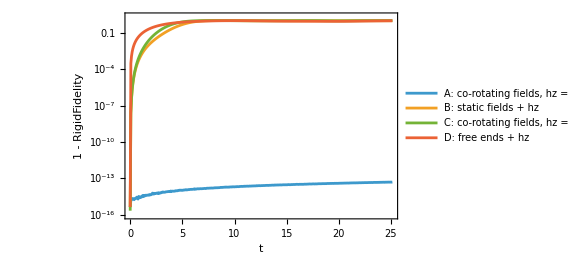

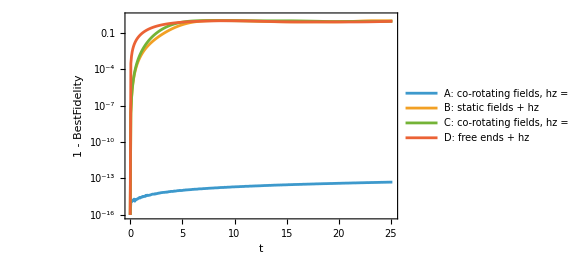

```mathematica
InfidelityPlot[Values[simulations], Keys[simulations], "RigidFidelity"]

InfidelityPlot[Values[simulations], Keys[simulations], "BestFidelity"]
```

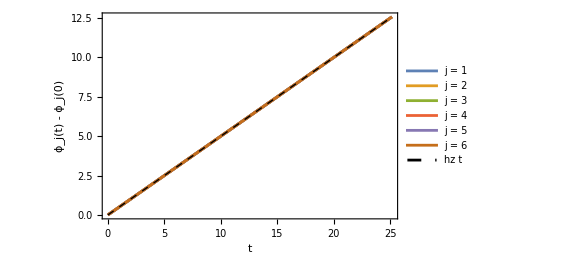

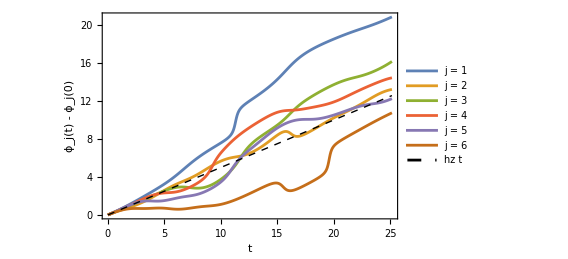

```mathematica
AzimuthPlot[simulations[[1]]]

AzimuthPlot[simulations[[4]]]
```

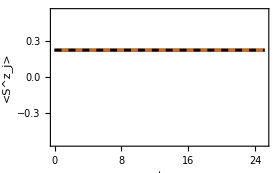
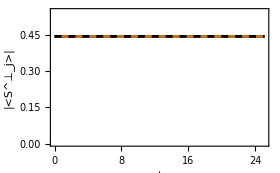
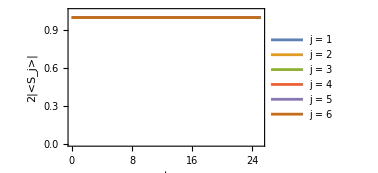

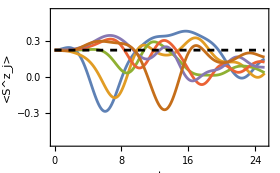
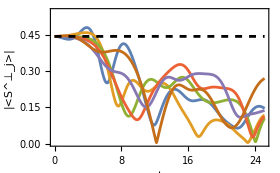
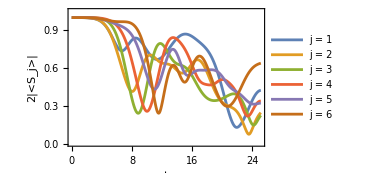

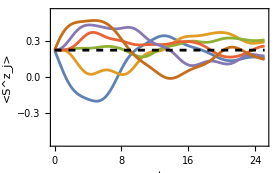
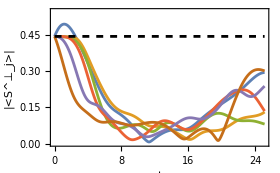

```mathematica
SiteObservablesPlot[simulations[[1]]]

SiteObservablesPlot[simulations[[2]]]

SiteObservablesPlot[simulations[[4]]]
```

Snapshots at t = 0, T/4, T/2, 3T/4, T with T = 2 Pi / w. Three-dimensional view: site j sits at height 1.5 j on the vertical axis and the arrow is 2<S_j>. Top view: the transverse Bloch vectors 2<S^perp_j> seen from the +z axis (outer circle: radius 1; inner circle: radius sin theta, where a rigid helix must stay). In A the fan of arrows turns as one body with fixed relative angles q; in D the arrows shrink and lose the common winding.

-Graphics-

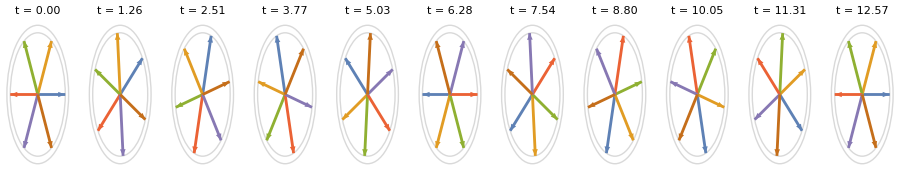

-Graphics-

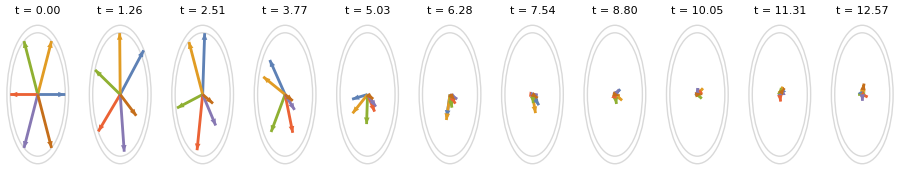

```mathematica
SnapshotRow[simulations[[1]], Subdivide[0., 2 Pi/omegaDrive, 10]]

TopViewRow[simulations[[1]], Subdivide[0., 2 Pi/omegaDrive, 10]]

SnapshotRow[simulations[[4]], Subdivide[0., 2 Pi/omegaDrive, 10]]

TopViewRow[simulations[[4]], Subdivide[0., 2 Pi/omegaDrive, 10]]
```

```mathematica
HelixAnimation[simulations[[1]], 100]
```

```mathematica
HelixAnimation[simulations[[2]], 100]
```

```mathematica
GraphicsRow[{EdgeBlochPlot[simulations[[1]]], EdgeBlochPlot[simulations[[2]]], EdgeBlochPlot[simulations[[3]]],EdgeBlochPlot[simulations[[4]]]}, ImageSize -> 1000]
```

-Graphics-

In A both edge Bloch vectors stay on the sphere and trace the latitude circle z = cos(theta), the edge spin being a pure rotating state. In B and D they move into the interior of the sphere.

### 4.4 Sensitivity of rigidity to the matching conditions

Maximum over two periods of 1 - BestFidelity, as a function of the detuning hz - w (at Delta = cos q) and of the anisotropy mismatch Delta - cos q (at hz = w). Both conditions are sharp: the infidelity is at machine precision only at zero mismatch, and over two periods it already reaches about 0.11 at |hz - w| = 0.02 and about 0.03 at |Delta - cos q| = 0.02. The scan uses the exact rotating-frame solution, which is valid for any parameters because H(t) = U(w t) H(0) U(w t)^dagger holds for every Delta and hz.

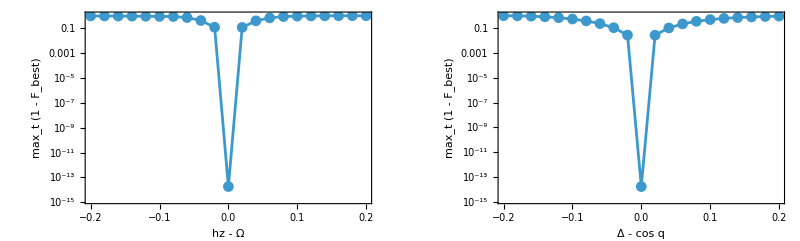

```mathematica
scanDetuning = InfidelityScan[protocols[[1]], "hz", omegaDrive + Subdivide[-0.2, 0.2, 20], tFinal, 120];
scanAnisotropy = InfidelityScan[protocols[[1]], "Delta", Cos[qWinding] + Subdivide[-0.2, 0.2, 20], tFinal, 120];
GraphicsRow[{ListLogPlot[Transpose[{scanDetuning[[All, 1]], Clip[scanDetuning[[All, 2]], {10^-16, 1}]}], Joined -> True, PlotMarkers -> Automatic, Frame -> True, FrameLabel -> {"hz - Ω", "max_t (1 - F_best)"}], ListLogPlot[Transpose[{scanAnisotropy[[All, 1]], Clip[scanAnisotropy[[All, 2]], {10^-16, 1}]}], Joined -> True, PlotMarkers -> Automatic, Frame -> True, FrameLabel -> {"Δ - cos q", "max_t (1 - F_best)"}]}, ImageSize -> 800]
```

### 4.5 Other system sizes

The construction is size-independent. Residual of the rotating-frame eigenvalue equation for n = 3, ..., 10, and a laboratory-frame simulation at n = 8 over one period.

```mathematica
Dataset[Table[<|"L" -> n, "RotatingFrameResidual" -> RigidityDiagnostics[RigidRotationProtocol[n, jCoupling, qWinding, thetaPolar, phiInitial, bLeft, bRight, omegaDrive]]["RotatingFrameResidual"]|>, {n, 3, 10}]]

SimulationSummary[Simulate[RigidRotationProtocol[8, jCoupling, qWinding, thetaPolar, phiInitial, bLeft, bRight, omegaDrive], 2 Pi/omegaDrive, 100]] // Dataset
```